```mathematica
(* asymptotic phase of the isochron clock
\dot{r}=r(1-r^2) \dot{\theta}=1+q(r^2-1)
transformed to 
\dot{R}=2R(1-R)
\dot{\theta} = 1 + q (R-1)
where R=r^2
*)
(* solution should be R[t_]= (a c Exp[ 2 a t])/(1+c Exp[2 a t]), c=R0/(a-R0) *)
(* check that the solution works: *)
R[t_]= Simplify[(a c Exp[ 2 a t])/(1+c Exp[2 a t])/. c->R0/(a-R0)]/.a->1;
Simplify[DSolve[{RR'[t]==2RR[t](1-RR[t]),RR[0]==RR[0]},RR[t],t]]
Simplify[D[R[t],t]]
Simplify[2R[t](1-R[t])]
(*q=1;a=1;θ0=0;*)
(*Plot3D[q/2 Log[(x^2+y^2)/a]+ArcTan[x/y],{x,-1,1},{y,-1,1}]*)
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument SuperscriptBox[True.

DSolve[{RR'[t]==-2 (-1+RR[t]) RR[t],True},RR[t],t]

-(2 ⅇ^(2 t) (-1+R0) R0)/((1+(-1+ⅇ^(2 t)) R0)^2)

-(2 ⅇ^(2 t) (-1+R0) R0)/((1+(-1+ⅇ^(2 t)) R0)^2)

```mathematica
(* calculate phase function (pg 170 nb#1) *)
Clear[θ,q,q,θ0]
FullSimplify[DSolve[{θ'[t]==1+q (R[t]-1),θ[0]==θ0},θ[t],t]]
```

{{θ[t]→t-q t+θ0+1/2 q Log[1+(-1+ⅇ^(2 t)) R0]}}

```mathematica
(* symptotic phase abs(theta(t) - t) (pg 170 nb#1*)
Clear[q,a,θ0,x,y]
F[x_,y_]:=q/2 Log[x^2+y^2]+ArcTan[y/x]-ArcTan[xLC/yLC];
```

```mathematica
Simplify[Grad[F[x,y],{x,y}]]
```

{(q x-y)/(x^2+y^2),(x+q y)/(x^2+y^2)}

```mathematica
(* solutions *)
θ[t_]:=t(1+q )+θ0;
x[t_]:=Cos[t];
y[t_]:= Sin[t];
```

```mathematica
(* PRC *)
a=1;q=5;θ0=0;
Z[t_]:=1/q{(q x[θ[t]]-y[θ[t]])/a,(x[θ[t]]+q y[θ[t]])/a};
Plot[{Z[t][[1]],Z[t][[2]]},{t,0,(2Pi)/(1+q a)}]

(* Plot[{Sqrt[a](Sin[θ[t]])/a, Sqrt[a](-Cos[θ[t]])/a},{t,0,(2Pi)/(1+q a)}] *)
```

-Graphics-

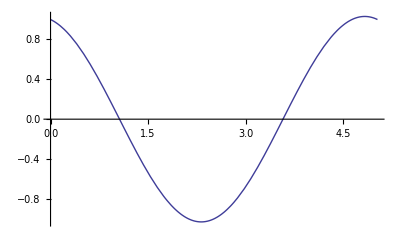

```mathematica
Plot[q Cos[θ[t]]-a Sin[θ[t]],{t,0,(2Pi)/(1+q a)}]
```